```mathematica
partitions=Map[#[[2]]&,{{4,{1,1,1,1},4,4,28995},
{5,{2,1,1,1},55,375,28991},
{6,{2,1,1,1,1},40,240,28898},
{9,{3,2,1,1,1,1},480,16258,28850},
{9,{2,2,2,1,1,1},24,216,28352},
{10,{3,2,2,1,1,1},240,8617,28345},
{12,{3,2,2,2,1,1,1},119,4179,28022},
{13,{4,3,2,1,1,1,1},1581,201101,27871},
{13,{4,2,2,2,1,1,1},84,6143,26067},
{14,{4,3,2,2,1,1,1},715,92156,26031},
{15,{3,3,3,2,1,1,1,1},69,2846,25558},
{15,{4,2,2,2,2,1,1,1},61,5485,25549},
{16,{4,3,2,2,2,1,1,1},383,51060,25537},
{16,{3,3,3,2,2,1,1,1},49,2272,25245},
{17,{5,3,3,2,1,1,1,1},256,53968,25237},
{17,{5,3,2,2,2,1,1,1},194,37273,23571},
{18,{5,4,3,2,1,1,1,1},1212,397759,23002},
{18,{5,4,2,2,2,1,1,1},141,35806,21377},
{18,{5,3,3,2,2,1,1,1},141,28108,21252},
{19,{5,4,3,2,2,1,1,1},613,211106,21217},
{19,{4,3,3,3,2,1,1,1,1},170,24381,20857},
{20,{5,3,3,3,2,1,1,1,1},85,15910,20839},
{20,{5,4,2,2,2,2,1,1,1},74,17405,20807},
{20,{4,3,3,3,2,2,1,1,1},77,10554,20750},
{21,{6,4,3,2,2,1,1,1,1},261,129601,20735},
{21,{6,3,3,3,2,1,1,1,1},62,18352,18484},
{21,{4,4,4,3,2,1,1,1,1},97,15803,18251},
{21,{6,4,2,2,2,2,1,1,1},49,15483,18227},
{21,{6,3,3,2,2,2,1,1,1},45,11861,18169},
{21,{5,4,3,2,2,2,1,1,1},243,75450,18140},
{21,{4,4,4,2,2,2,1,1,1},12,1392,18083},
{21,{5,3,3,3,2,2,1,1,1},50,10088,18081},
{22,{6,4,3,3,2,1,1,1,1},222,114389,18062},
{22,{6,4,3,2,2,2,1,1,1},191,96179,17698},
{22,{6,3,3,3,2,2,1,1,1},40,10844,17379},
{22,{4,4,4,3,2,2,1,1,1},68,12222,17352},
{23,{6,5,3,3,2,1,1,1,1},105,57287,17331},
{23,{6,4,4,3,2,1,1,1,1},165,90540,16649},
{23,{6,5,3,2,2,2,1,1,1},107,60817,16498},
{23,{6,4,4,2,2,2,1,1,1},30,13984,16256},
{23,{6,4,3,3,2,2,1,1,1},95,46228,16216},
{24,{6,5,4,3,2,1,1,1,1},303,224382,16150},
{24,{6,5,4,2,2,2,1,1,1},64,40807,15623},
{24,{6,5,3,3,2,2,1,1,1},64,36143,15504},
{24,{6,4,4,3,2,2,1,1,1},71,39894,15477},
{24,{6,3,3,3,3,2,1,1,1,1},31,8549,15437},
{25,{7,5,4,3,2,1,1,1,1},191,169768,15431},
{25,{7,5,4,2,2,2,1,1,1},43,34354,11840},
{25,{7,5,3,3,2,2,1,1,1},43,29241,11565},
{25,{7,4,4,3,2,2,1,1,1},51,33420,11455},
{25,{6,5,4,3,2,2,1,1,1},149,117642,11378},
{25,{7,3,3,3,3,2,1,1,1,1},25,10822,11287},
{25,{6,4,3,3,3,2,1,1,1,1},54,26779,11257},
{25,{6,3,3,3,3,2,2,1,1,1},22,7244,11241},
{26,{7,5,4,3,2,2,1,1,1},101,97083,11239},
{26,{7,4,3,3,3,2,1,1,1,1},35,18883,10817},
{26,{6,5,3,3,3,2,1,1,1,1},43,24172,10764},
{26,{5,4,4,4,3,2,1,1,1,1},57,22284,10738},
{26,{7,4,4,2,2,2,2,1,1,1},12,5955,10718},
{26,{6,5,4,2,2,2,2,1,1,1},30,19547,10698},
{26,{5,4,4,4,2,2,2,1,1,1},12,3830,10664},
{26,{7,3,3,3,3,2,2,1,1,1},13,5231,10660},
{26,{6,4,3,3,3,2,2,1,1,1},29,13835,10648},
{27,{7,5,3,3,3,2,1,1,1,1},31,20627,10634},
{27,{7,4,4,3,3,2,1,1,1,1},22,14029,10611},
{27,{5,5,5,3,3,2,1,1,1,1},14,4200,10597},
{27,{6,4,4,4,3,2,1,1,1,1},40,24644,10586},
{27,{7,5,4,2,2,2,2,1,1,1},19,14672,10566},
{27,{7,5,3,3,2,2,2,1,1,1},19,12438,10534},
{27,{7,4,4,3,2,2,2,1,1,1},22,15103,10528},
{27,{6,5,4,3,2,2,2,1,1,1},49,36051,10521},
{27,{5,5,5,3,2,2,2,1,1,1},12,3520,10507},
{27,{6,4,4,4,2,2,2,1,1,1},9,4014,10505},
{27,{7,4,3,3,3,2,2,1,1,1},25,16831,10500},
{27,{6,5,3,3,3,2,2,1,1,1},19,11772,10486},
{27,{5,4,4,4,3,2,2,1,1,1},31,12696,10476},
{28,{7,6,4,3,2,2,1,1,1,1},30,32570,10468},
{28,{7,6,3,3,3,2,1,1,1,1},18,14098,10115},
{28,{7,4,4,4,3,2,1,1,1,1},29,20215,10006},
{28,{5,5,5,4,3,2,1,1,1,1},46,21484,9985},
{28,{7,6,4,2,2,2,2,1,1,1},15,14848,9969},
{28,{7,6,3,3,2,2,2,1,1,1},15,11343,9901},
{28,{7,5,4,3,2,2,2,1,1,1},37,33439,9888},
{28,{7,4,4,4,2,2,2,1,1,1},9,5865,9884},
{28,{5,5,5,4,2,2,2,1,1,1},11,4035,9880},
{28,{7,5,3,3,3,2,2,1,1,1},15,10357,9877},
{28,{5,5,5,3,3,2,2,1,1,1},11,3915,9870},
{28,{6,4,4,4,3,2,2,1,1,1},25,15712,9868},
{29,{8,6,4,3,2,2,1,1,1,1},22,28001,9861},
{29,{8,6,3,3,3,2,1,1,1,1},11,11705,7730},
{29,{8,5,4,3,3,2,1,1,1,1},22,24078,7560},
{29,{7,6,4,3,3,2,1,1,1,1},20,21392,7218},
{29,{7,5,5,3,3,2,1,1,1,1},12,10501,7153},
{29,{8,4,4,4,3,2,1,1,1,1},22,17197,7110},
{29,{8,6,4,2,2,2,2,1,1,1},11,12621,7038},
{29,{8,6,3,3,2,2,2,1,1,1},13,13505,6922},
{29,{8,5,4,3,2,2,2,1,1,1},25,27383,6902},
{29,{7,6,4,3,2,2,2,1,1,1},23,23919,6826},
{29,{7,5,5,3,2,2,2,1,1,1},13,9554,6795},
{29,{8,4,4,4,2,2,2,1,1,1},7,5159,6786},
{29,{8,5,3,3,3,2,2,1,1,1},13,12011,6780},
{29,{7,6,3,3,3,2,2,1,1,1},11,8663,6766},
{29,{8,4,4,3,3,2,2,1,1,1},11,8759,6753},
{29,{7,4,4,4,3,2,2,1,1,1},13,8377,6748},
{29,{5,5,5,4,3,2,2,1,1,1},19,9051,6745},
{30,{8,6,4,3,3,2,1,1,1,1},18,25368,6740},
{30,{8,5,5,3,3,2,1,1,1,1},10,10750,6209},
{30,{7,6,5,3,3,2,1,1,1,1},16,19290,6131},
{30,{8,5,4,4,3,2,1,1,1,1},18,22261,6023},
{30,{7,6,4,4,3,2,1,1,1,1},16,18543,5927},
{30,{8,6,4,3,2,2,2,1,1,1},13,17632,5884},
{30,{8,5,5,3,2,2,2,1,1,1},7,7287,5768},
{30,{7,6,5,3,2,2,2,1,1,1},13,15537,5737},
{30,{8,5,4,4,2,2,2,1,1,1},8,10145,5708},
{30,{7,6,4,4,2,2,2,1,1,1},6,7214,5678},
{30,{8,6,3,3,3,2,2,1,1,1},7,7925,5645},
{30,{8,5,4,3,3,2,2,1,1,1},15,17851,5627},
{30,{7,6,4,3,3,2,2,1,1,1},13,14222,5613},
{30,{8,4,4,4,3,2,2,1,1,1},11,9776,5605},
{31,{8,6,5,3,3,2,1,1,1,1},11,16363,5598},
{31,{8,6,4,4,3,2,1,1,1,1},12,15509,5495},
{31,{8,5,5,4,3,2,1,1,1,1},16,19798,5463},
{31,{7,6,5,4,3,2,1,1,1,1},21,30013,5449},
{31,{8,6,5,3,2,2,2,1,1,1},8,11030,5376},
{31,{8,6,4,4,2,2,2,1,1,1},4,5285,5333},
{31,{8,5,5,4,2,2,2,1,1,1},6,6414,5318},
{31,{7,6,5,4,2,2,2,1,1,1},9,12641,5314},
{31,{8,6,4,3,3,2,2,1,1,1},10,13449,5281},
{31,{8,5,5,3,3,2,2,1,1,1},6,5821,5269},
{31,{7,6,5,3,3,2,2,1,1,1},9,11186,5267},
{31,{8,5,4,4,3,2,2,1,1,1},11,12567,5257},
{31,{7,6,4,4,3,2,2,1,1,1},12,14817,5235},
{31,{7,6,3,3,3,3,2,1,1,1,1},8,6042,5229},
{32,{8,6,5,4,3,2,1,1,1,1},14,25288,5207},
{32,{8,6,5,4,2,2,2,1,1,1},6,10635,5089},
{32,{8,6,5,3,3,2,2,1,1,1},6,10199,5047},
{32,{8,6,4,4,3,2,2,1,1,1},7,10716,5038},
{32,{8,5,5,4,3,2,2,1,1,1},7,8691,5033},
{32,{7,6,5,4,3,2,2,1,1,1},9,13147,5031},
{32,{8,6,3,3,3,3,2,1,1,1,1},7,6698,5023},
{32,{7,6,4,3,3,3,2,1,1,1,1},10,10689,5012},
{32,{7,4,4,4,4,3,2,1,1,1,1},9,6282,5006},
{32,{7,4,4,4,4,2,2,2,1,1,1},3,1803,5000},
{32,{7,6,3,3,3,3,2,2,1,1,1},4,3300,4999},
{33,{9,6,5,4,3,2,1,1,1,1},8,17273,4995},
{33,{8,7,5,4,3,2,1,1,1,1},8,15995,3395},
{33,{9,6,5,4,2,2,2,1,1,1},4,8242,3168},
{33,{8,7,5,4,2,2,2,1,1,1},4,7512,3061},
{33,{9,6,5,3,3,2,2,1,1,1},4,7381,3036},
{33,{8,7,5,3,3,2,2,1,1,1},4,6875,3018},
{33,{9,6,4,4,3,2,2,1,1,1},4,6579,3009},
{33,{8,7,4,4,3,2,2,1,1,1},4,6065,2981},
{33,{9,5,5,4,3,2,2,1,1,1},5,7793,2970},
{33,{8,6,5,4,3,2,2,1,1,1},6,11444,2953},
{33,{6,6,6,4,3,2,2,1,1,1,1},5,4735,2947},
{33,{9,6,3,3,3,3,2,1,1,1,1},3,2848,2926},
{33,{8,7,3,3,3,3,2,1,1,1,1},3,2604,2906},
{33,{8,6,4,3,3,3,2,1,1,1,1},4,4786,2897},
{33,{8,5,5,3,3,3,2,1,1,1,1},3,2718,2895},
{33,{7,6,5,3,3,3,2,1,1,1,1},4,4300,2893},
{33,{6,6,6,3,3,3,2,1,1,1,1},3,2039,2887},
{33,{9,4,4,4,3,3,2,1,1,1,1},3,2556,2885},
{33,{6,5,5,5,3,3,2,1,1,1,1},3,2044,2880},
{33,{8,4,4,4,4,3,2,1,1,1,1},6,5490,2871},
{33,{6,6,6,4,2,2,2,2,1,1,1},3,2569,2863},
{33,{6,6,6,3,3,2,2,2,1,1,1},2,1326,2861},
{33,{6,5,5,5,3,2,2,2,1,1,1},3,2171,2860},
{33,{8,4,4,4,4,2,2,2,1,1,1},2,1398,2858},
{33,{8,6,3,3,3,3,2,2,1,1,1},3,2696,2857},
{33,{7,6,4,3,3,3,2,2,1,1,1},4,4136,2855},
{34,{9,7,5,4,3,2,1,1,1,1},5,11451,2854},
{34,{9,7,5,4,2,2,2,1,1,1},3,6630,2260},
{34,{9,7,5,3,3,2,2,1,1,1},3,5643,2205},
{34,{9,7,4,4,3,2,2,1,1,1},4,7910,2188},
{34,{9,6,5,4,3,2,2,1,1,1},5,11447,2173},
{34,{8,7,5,4,3,2,2,1,1,1},5,10569,2156},
{34,{9,7,3,3,3,3,2,1,1,1,1},3,3375,2148},
{34,{9,6,4,3,3,3,2,1,1,1,1},4,6193,2135},
{34,{8,7,4,3,3,3,2,1,1,1,1},4,5720,2121},
{34,{9,5,5,3,3,3,2,1,1,1,1},3,3407,2117},
{34,{8,6,5,3,3,3,2,1,1,1,1},3,3877,2115},
{34,{6,6,6,4,3,3,2,1,1,1,1},4,4122,2111},
{34,{7,5,5,5,3,3,2,1,1,1,1},3,2736,2107},
{34,{9,4,4,4,4,3,2,1,1,1,1},4,4094,2098},
{34,{8,5,4,4,4,3,2,1,1,1,1},4,4931,2074},
{34,{7,6,4,4,4,3,2,1,1,1,1},4,4792,2069},
{34,{6,5,5,5,4,3,2,1,1,1,1},5,4868,2064},
{34,{9,6,4,4,2,2,2,2,1,1,1},2,2624,2059},
{34,{8,7,4,4,2,2,2,2,1,1,1},2,2406,2052},
{34,{8,6,5,4,2,2,2,2,1,1,1},3,4721,2046},
{34,{6,6,6,4,3,2,2,2,1,1,1},4,4312,2044},
{34,{7,5,5,5,3,2,2,2,1,1,1},3,2921,2042},
{34,{9,4,4,4,4,2,2,2,1,1,1},2,1778,2040},
{34,{8,5,4,4,4,2,2,2,1,1,1},2,2092,2037},
{34,{7,6,4,4,4,2,2,2,1,1,1},2,2066,2036},
{34,{6,5,5,5,4,2,2,2,1,1,1},3,2786,2035},
{34,{9,6,3,3,3,3,2,2,1,1,1},3,3500,2033},
{34,{8,7,3,3,3,3,2,2,1,1,1},3,3192,2028},
{34,{8,6,4,3,3,3,2,2,1,1,1},4,5778,2026},
{34,{6,6,6,3,3,3,2,2,1,1,1},3,2479,2025},
{34,{6,5,5,5,3,3,2,2,1,1,1},3,2504,2024},
{34,{8,4,4,4,4,3,2,2,1,1,1},4,3891,2023},
{35,{9,7,5,4,3,2,2,1,1,1},3,7390,2022},
{35,{9,7,4,3,3,3,2,1,1,1,1},2,3337,1937},
{35,{9,6,5,3,3,3,2,1,1,1,1},2,3407,1925},
{35,{8,7,5,3,3,3,2,1,1,1,1},2,3179,1919},
{35,{9,6,4,4,3,3,2,1,1,1,1},2,3518,1917},
{35,{8,7,4,4,3,3,2,1,1,1,1},2,3253,1915},
{35,{9,5,5,4,3,3,2,1,1,1,1},2,3092,1911},
{35,{8,5,5,5,3,3,2,1,1,1,1},2,2612,1909},
{35,{6,6,6,5,3,3,2,1,1,1,1},2,2174,1900},
{35,{9,5,4,4,4,3,2,1,1,1,1},3,4887,1891},
{35,{8,6,4,4,4,3,2,1,1,1,1},3,5110,1881},
{35,{6,6,6,4,4,3,2,1,1,1,1},3,3649,1871},
{35,{7,5,5,5,4,3,2,1,1,1,1},3,3791,1866},
{35,{9,7,4,4,2,2,2,2,1,1,1},2,3186,1861},
{35,{9,6,5,4,2,2,2,2,1,1,1},2,3384,1841},
{35,{8,7,5,4,2,2,2,2,1,1,1},2,3082,1837},
{35,{9,6,5,3,3,2,2,2,1,1,1},2,3258,1833},
{35,{8,7,5,3,3,2,2,2,1,1,1},2,3032,1829},
{35,{9,6,4,4,3,2,2,2,1,1,1},3,5455,1827},
{35,{8,7,4,4,3,2,2,2,1,1,1},3,5022,1826},
{35,{8,6,5,4,3,2,2,2,1,1,1},3,5443,1825},
{35,{8,5,5,5,3,2,2,2,1,1,1},3,4006,1823},
{35,{6,6,6,5,3,2,2,2,1,1,1},3,3357,1821},
{35,{9,5,4,4,4,2,2,2,1,1,1},2,2726,1819},
{35,{8,6,4,4,4,2,2,2,1,1,1},2,2848,1817},
{35,{6,6,6,4,4,2,2,2,1,1,1},2,2046,1813},
{35,{7,5,5,5,4,2,2,2,1,1,1},2,2096,1812},
{35,{9,7,3,3,3,3,2,2,1,1,1},2,2514,1810},
{35,{9,6,4,3,3,3,2,2,1,1,1},2,3030,1808},
{35,{8,7,4,3,3,3,2,2,1,1,1},2,2790,1807},
{35,{9,5,5,3,3,3,2,2,1,1,1},2,2538,1806},
{35,{8,6,5,3,3,3,2,2,1,1,1},2,2882,1805},
{35,{6,6,6,4,3,3,2,2,1,1,1},2,2026,1803},
{35,{7,5,5,5,3,3,2,2,1,1,1},2,2036,1802},
{35,{9,4,4,4,4,3,2,2,1,1,1},3,3519,1801},
{35,{8,5,4,4,4,3,2,2,1,1,1},3,4244,1798},
{35,{7,6,4,4,4,3,2,2,1,1,1},3,4133,1797},
{35,{6,5,5,5,4,3,2,2,1,1,1},3,3115,1796},
{36,{9,6,6,4,3,2,2,1,1,1,1},1,2143,1795},
{36,{8,7,6,4,3,2,2,1,1,1,1},1,2116,1774},
{36,{9,7,5,3,3,3,2,1,1,1,1},2,4088,1753},
{36,{9,6,6,3,3,3,2,1,1,1,1},2,4017,1749},
{36,{8,7,6,3,3,3,2,1,1,1,1},2,3937,1721},
{36,{9,7,4,4,3,3,2,1,1,1,1},2,4212,1717},
{36,{9,5,5,5,3,3,2,1,1,1,1},2,3305,1713},
{36,{9,6,4,4,4,3,2,1,1,1,1},2,4080,1704},
{36,{8,7,4,4,4,3,2,1,1,1,1},2,3773,1694},
{36,{9,5,5,4,4,3,2,1,1,1,1},2,3726,1684},
{36,{8,5,5,5,4,3,2,1,1,1,1},2,3207,1674},
{36,{6,6,6,5,4,3,2,1,1,1,1},2,2730,1669},
{36,{9,7,5,4,2,2,2,2,1,1,1},1,2083,1664},
{36,{9,6,6,4,2,2,2,2,1,1,1},1,1996,1645},
{36,{8,7,6,4,2,2,2,2,1,1,1},1,1985,1636},
{36,{9,7,5,3,3,2,2,2,1,1,1},1,1978,1631},
{36,{9,6,6,3,3,2,2,2,1,1,1},1,1913,1629},
{36,{8,7,6,3,3,2,2,2,1,1,1},1,1891,1626},
{36,{9,7,4,4,3,2,2,2,1,1,1},1,1969,1624},
{36,{9,6,5,4,3,2,2,2,1,1,1},1,2112,1623},
{36,{8,7,5,4,3,2,2,2,1,1,1},1,1946,1621},
{36,{9,5,5,5,3,2,2,2,1,1,1},1,1535,1619},
{36,{9,6,4,4,4,2,2,2,1,1,1},1,1832,1617},
{36,{8,7,4,4,4,2,2,2,1,1,1},1,1683,1614},
{36,{9,5,5,4,4,2,2,2,1,1,1},1,1671,1610},
{36,{8,5,5,5,4,2,2,2,1,1,1},1,1402,1608},
{36,{6,6,6,5,4,2,2,2,1,1,1},1,1233,1606},
{36,{9,7,4,3,3,3,2,2,1,1,1},1,1808,1604},
{36,{9,6,5,3,3,3,2,2,1,1,1},1,1846,1603},
{36,{8,7,5,3,3,3,2,2,1,1,1},1,1722,1601},
{36,{8,5,5,5,3,3,2,2,1,1,1},1,1412,1600},
{36,{6,6,6,5,3,3,2,2,1,1,1},1,1171,1599},
{36,{9,5,4,4,4,3,2,2,1,1,1},1,1635,1598},
{36,{8,6,4,4,4,3,2,2,1,1,1},1,1711,1597},
{36,{6,6,6,4,4,3,2,2,1,1,1},1,1223,1595},
{36,{7,5,5,5,4,3,2,2,1,1,1},1,1269,1594},
{37,{10,7,5,4,3,2,2,1,1,1,1},1,2906,1593},
{37,{10,6,6,4,3,2,2,1,1,1,1},1,2785,1250},
{37,{9,7,6,4,3,2,2,1,1,1,1},1,2786,1180},
{37,{10,7,5,3,3,3,2,1,1,1,1},1,2503,1159},
{37,{10,6,6,3,3,3,2,1,1,1,1},1,2358,1138},
{37,{9,7,6,3,3,3,2,1,1,1,1},1,2367,1124},
{37,{10,7,4,4,3,3,2,1,1,1,1},1,2626,1116},
{37,{10,6,5,4,3,3,2,1,1,1,1},1,2701,1110},
{37,{9,6,6,4,3,3,2,1,1,1,1},1,2459,1105},
{37,{8,7,6,4,3,3,2,1,1,1,1},1,2417,1102},
{37,{10,5,5,5,3,3,2,1,1,1,1},1,1966,1098},
{37,{9,6,5,5,3,3,2,1,1,1,1},1,2311,1071},
{37,{8,7,5,5,3,3,2,1,1,1,1},1,2156,1060},
{37,{10,6,4,4,4,3,2,1,1,1,1},1,2491,1051},
{37,{9,7,4,4,4,3,2,1,1,1,1},1,2259,1034},
{37,{10,5,5,4,4,3,2,1,1,1,1},1,2192,1029},
{37,{9,5,5,5,4,3,2,1,1,1,1},1,1896,1024},
{37,{10,7,5,4,2,2,2,2,1,1,1},1,2689,1017},
{37,{10,6,6,4,2,2,2,2,1,1,1},1,2603,995},
{37,{9,7,6,4,2,2,2,2,1,1,1},1,2622,980},
{37,{10,7,5,3,3,2,2,2,1,1,1},1,2613,975},
{37,{10,6,6,3,3,2,2,2,1,1,1},1,2440,970},
{37,{9,7,6,3,3,2,2,2,1,1,1},1,2485,967},
{37,{10,7,4,4,3,2,2,2,1,1,1},1,2634,965},
{37,{10,6,5,4,3,2,2,2,1,1,1},1,2731,963},
{37,{9,7,5,4,3,2,2,2,1,1,1},1,2576,961},
{37,{9,6,6,4,3,2,2,2,1,1,1},1,2486,959},
{37,{8,7,6,4,3,2,2,2,1,1,1},1,2456,957},
{37,{10,5,5,5,3,2,2,2,1,1,1},1,1976,955},
{37,{9,6,5,5,3,2,2,2,1,1,1},1,2344,950},
{37,{8,7,5,5,3,2,2,2,1,1,1},1,2169,947},
{37,{10,6,4,4,4,2,2,2,1,1,1},1,2428,945},
{37,{9,7,4,4,4,2,2,2,1,1,1},1,2215,942},
{37,{10,5,5,4,4,2,2,2,1,1,1},1,2116,940},
{37,{9,5,5,5,4,2,2,2,1,1,1},1,1843,939},
{37,{10,7,4,3,3,3,2,2,1,1,1},1,2448,937},
{37,{10,6,5,3,3,3,2,2,1,1,1},1,2379,935},
{37,{9,7,5,3,3,3,2,2,1,1,1},1,2222,933},
{37,{9,6,6,3,3,3,2,2,1,1,1},1,2170,932},
{37,{8,7,6,3,3,3,2,2,1,1,1},1,2129,928},
{37,{10,6,4,4,3,3,2,2,1,1,1},1,2506,926},
{37,{10,5,5,4,3,3,2,2,1,1,1},1,2152,925},
{37,{9,5,5,5,3,3,2,2,1,1,1},1,1790,924},
{37,{10,5,4,4,4,3,2,2,1,1,1},1,2097,923},
{37,{9,6,4,4,4,3,2,2,1,1,1},1,2201,922},
{37,{8,7,4,4,4,3,2,2,1,1,1},1,2032,921},
{37,{8,5,5,5,4,3,2,2,1,1,1},1,1727,919},
{37,{6,6,6,5,4,3,2,2,1,1,1},1,1471,918},
{38,{10,7,6,4,3,2,2,1,1,1,1},1,3689,917},
{38,{9,8,6,4,3,2,2,1,1,1,1},1,3495,435},
{38,{10,7,6,3,3,3,2,1,1,1,1},1,3119,329},
{38,{9,8,6,3,3,3,2,1,1,1,1},1,3043,296},
{38,{10,7,5,4,3,3,2,1,1,1,1},1,3343,286},
{38,{9,8,5,4,3,3,2,1,1,1,1},1,3152,271},
{38,{10,6,6,4,3,3,2,1,1,1,1},1,3188,266},
{38,{9,7,6,4,3,3,2,1,1,1,1},1,3176,261},
{38,{10,6,5,5,3,3,2,1,1,1,1},1,2989,256},
{38,{9,7,5,5,3,3,2,1,1,1,1},1,2785,236},
{38,{9,6,6,5,3,3,2,1,1,1,1},1,2881,227},
{38,{8,7,6,5,3,3,2,1,1,1,1},1,2845,216},
{38,{10,7,4,4,4,3,2,1,1,1,1},1,3045,205},
{38,{9,8,4,4,4,3,2,1,1,1,1},1,2757,179},
{38,{10,6,5,4,4,3,2,1,1,1,1},1,3262,169},
{38,{9,6,6,4,4,3,2,1,1,1,1},1,2956,159},
{38,{8,7,6,4,4,3,2,1,1,1,1},1,2912,154},
{38,{10,5,5,5,4,3,2,1,1,1,1},1,2426,149},
{38,{10,7,6,4,2,2,2,2,1,1,1},1,3434,137},
{38,{9,8,6,4,2,2,2,2,1,1,1},1,3284,93},
{38,{10,7,6,3,3,2,2,2,1,1,1},1,3244,73},
{38,{9,8,6,3,3,2,2,2,1,1,1},1,3179,64},
{38,{10,7,5,4,3,2,2,2,1,1,1},1,3374,61},
{38,{9,8,5,4,3,2,2,2,1,1,1},1,3190,56},
{38,{10,6,6,4,3,2,2,2,1,1,1},1,3226,54},
{38,{9,7,6,4,3,2,2,2,1,1,1},1,3238,52},
{38,{10,6,5,5,3,2,2,2,1,1,1},1,3020,50},
{38,{9,7,5,5,3,2,2,2,1,1,1},1,2871,47},
{38,{9,6,6,5,3,2,2,2,1,1,1},1,2911,44},
{38,{8,7,6,5,3,2,2,2,1,1,1},1,2896,42},
{38,{10,7,4,4,4,2,2,2,1,1,1},1,2936,40},
{38,{9,8,4,4,4,2,2,2,1,1,1},1,2698,34},
{38,{10,6,5,4,4,2,2,2,1,1,1},1,3180,32},
{38,{9,6,6,4,4,2,2,2,1,1,1},1,2888,30},
{38,{8,7,6,4,4,2,2,2,1,1,1},1,2851,29},
{38,{10,5,5,5,4,2,2,2,1,1,1},1,2339,28},
{38,{10,7,5,3,3,3,2,2,1,1,1},1,2957,24},
{38,{9,8,5,3,3,3,2,2,1,1,1},1,2825,22},
{38,{10,6,6,3,3,3,2,2,1,1,1},1,2763,21},
{38,{9,7,6,3,3,3,2,2,1,1,1},1,2794,17},
{38,{10,7,4,4,3,3,2,2,1,1,1},1,3078,13},
{38,{9,8,4,4,3,3,2,2,1,1,1},1,2786,11},
{38,{10,6,5,4,3,3,2,2,1,1,1},1,3174,10},
{38,{9,6,6,4,3,3,2,2,1,1,1},1,2889,9},
{38,{8,7,6,4,3,3,2,2,1,1,1},1,2842,8},
{38,{10,5,5,5,3,3,2,2,1,1,1},1,2310,6},
{38,{10,6,4,4,4,3,2,2,1,1,1},1,2914,4},
{38,{9,7,4,4,4,3,2,2,1,1,1},1,2646,3},
{38,{10,5,5,4,4,3,2,2,1,1,1},1,2557,2},
{38,{9,5,5,5,4,3,2,2,1,1,1},1,2221,1}}]
```

{{1,1,1,1},{2,1,1,1},{2,1,1,1,1},{3,2,1,1,1,1},{2,2,2,1,1,1},{3,2,2,1,1,1},{3,2,2,2,1,1,1},{4,3,2,1,1,1,1},{4,2,2,2,1,1,1},{4,3,2,2,1,1,1},{3,3,3,2,1,1,1,1},{4,2,2,2,2,1,1,1},{4,3,2,2,2,1,1,1},{3,3,3,2,2,1,1,1},{5,3,3,2,1,1,1,1},{5,3,2,2,2,1,1,1},{5,4,3,2,1,1,1,1},{5,4,2,2,2,1,1,1},{5,3,3,2,2,1,1,1},{5,4,3,2,2,1,1,1},{4,3,3,3,2,1,1,1,1},{5,3,3,3,2,1,1,1,1},{5,4,2,2,2,2,1,1,1},{4,3,3,3,2,2,1,1,1},{6,4,3,2,2,1,1,1,1},{6,3,3,3,2,1,1,1,1},{4,4,4,3,2,1,1,1,1},{6,4,2,2,2,2,1,1,1},{6,3,3,2,2,2,1,1,1},{5,4,3,2,2,2,1,1,1},{4,4,4,2,2,2,1,1,1},{5,3,3,3,2,2,1,1,1},{6,4,3,3,2,1,1,1,1},{6,4,3,2,2,2,1,1,1},{6,3,3,3,2,2,1,1,1},{4,4,4,3,2,2,1,1,1},{6,5,3,3,2,1,1,1,1},{6,4,4,3,2,1,1,1,1},{6,5,3,2,2,2,1,1,1},{6,4,4,2,2,2,1,1,1},{6,4,3,3,2,2,1,1,1},{6,5,4,3,2,1,1,1,1},{6,5,4,2,2,2,1,1,1},{6,5,3,3,2,2,1,1,1},{6,4,4,3,2,2,1,1,1},{6,3,3,3,3,2,1,1,1,1},{7,5,4,3,2,1,1,1,1},{7,5,4,2,2,2,1,1,1},{7,5,3,3,2,2,1,1,1},{7,4,4,3,2,2,1,1,1},{6,5,4,3,2,2,1,1,1},{7,3,3,3,3,2,1,1,1,1},{6,4,3,3,3,2,1,1,1,1},{6,3,3,3,3,2,2,1,1,1},{7,5,4,3,2,2,1,1,1},{7,4,3,3,3,2,1,1,1,1},{6,5,3,3,3,2,1,1,1,1},{5,4,4,4,3,2,1,1,1,1},{7,4,4,2,2,2,2,1,1,1},{6,5,4,2,2,2,2,1,1,1},{5,4,4,4,2,2,2,1,1,1},{7,3,3,3,3,2,2,1,1,1},{6,4,3,3,3,2,2,1,1,1},{7,5,3,3,3,2,1,1,1,1},{7,4,4,3,3,2,1,1,1,1},{5,5,5,3,3,2,1,1,1,1},{6,4,4,4,3,2,1,1,1,1},{7,5,4,2,2,2,2,1,1,1},{7,5,3,3,2,2,2,1,1,1},{7,4,4,3,2,2,2,1,1,1},{6,5,4,3,2,2,2,1,1,1},{5,5,5,3,2,2,2,1,1,1},{6,4,4,4,2,2,2,1,1,1},{7,4,3,3,3,2,2,1,1,1},{6,5,3,3,3,2,2,1,1,1},{5,4,4,4,3,2,2,1,1,1},{7,6,4,3,2,2,1,1,1,1},{7,6,3,3,3,2,1,1,1,1},{7,4,4,4,3,2,1,1,1,1},{5,5,5,4,3,2,1,1,1,1},{7,6,4,2,2,2,2,1,1,1},{7,6,3,3,2,2,2,1,1,1},{7,5,4,3,2,2,2,1,1,1},{7,4,4,4,2,2,2,1,1,1},{5,5,5,4,2,2,2,1,1,1},{7,5,3,3,3,2,2,1,1,1},{5,5,5,3,3,2,2,1,1,1},{6,4,4,4,3,2,2,1,1,1},{8,6,4,3,2,2,1,1,1,1},{8,6,3,3,3,2,1,1,1,1},{8,5,4,3,3,2,1,1,1,1},{7,6,4,3,3,2,1,1,1,1},{7,5,5,3,3,2,1,1,1,1},{8,4,4,4,3,2,1,1,1,1},{8,6,4,2,2,2,2,1,1,1},{8,6,3,3,2,2,2,1,1,1},{8,5,4,3,2,2,2,1,1,1},{7,6,4,3,2,2,2,1,1,1},{7,5,5,3,2,2,2,1,1,1},{8,4,4,4,2,2,2,1,1,1},{8,5,3,3,3,2,2,1,1,1},{7,6,3,3,3,2,2,1,1,1},{8,4,4,3,3,2,2,1,1,1},{7,4,4,4,3,2,2,1,1,1},{5,5,5,4,3,2,2,1,1,1},{8,6,4,3,3,2,1,1,1,1},{8,5,5,3,3,2,1,1,1,1},{7,6,5,3,3,2,1,1,1,1},{8,5,4,4,3,2,1,1,1,1},{7,6,4,4,3,2,1,1,1,1},{8,6,4,3,2,2,2,1,1,1},{8,5,5,3,2,2,2,1,1,1},{7,6,5,3,2,2,2,1,1,1},{8,5,4,4,2,2,2,1,1,1},{7,6,4,4,2,2,2,1,1,1},{8,6,3,3,3,2,2,1,1,1},{8,5,4,3,3,2,2,1,1,1},{7,6,4,3,3,2,2,1,1,1},{8,4,4,4,3,2,2,1,1,1},{8,6,5,3,3,2,1,1,1,1},{8,6,4,4,3,2,1,1,1,1},{8,5,5,4,3,2,1,1,1,1},{7,6,5,4,3,2,1,1,1,1},{8,6,5,3,2,2,2,1,1,1},{8,6,4,4,2,2,2,1,1,1},{8,5,5,4,2,2,2,1,1,1},{7,6,5,4,2,2,2,1,1,1},{8,6,4,3,3,2,2,1,1,1},{8,5,5,3,3,2,2,1,1,1},{7,6,5,3,3,2,2,1,1,1},{8,5,4,4,3,2,2,1,1,1},{7,6,4,4,3,2,2,1,1,1},{7,6,3,3,3,3,2,1,1,1,1},{8,6,5,4,3,2,1,1,1,1},{8,6,5,4,2,2,2,1,1,1},{8,6,5,3,3,2,2,1,1,1},{8,6,4,4,3,2,2,1,1,1},{8,5,5,4,3,2,2,1,1,1},{7,6,5,4,3,2,2,1,1,1},{8,6,3,3,3,3,2,1,1,1,1},{7,6,4,3,3,3,2,1,1,1,1},{7,4,4,4,4,3,2,1,1,1,1},{7,4,4,4,4,2,2,2,1,1,1},{7,6,3,3,3,3,2,2,1,1,1},{9,6,5,4,3,2,1,1,1,1},{8,7,5,4,3,2,1,1,1,1},{9,6,5,4,2,2,2,1,1,1},{8,7,5,4,2,2,2,1,1,1},{9,6,5,3,3,2,2,1,1,1},{8,7,5,3,3,2,2,1,1,1},{9,6,4,4,3,2,2,1,1,1},{8,7,4,4,3,2,2,1,1,1},{9,5,5,4,3,2,2,1,1,1},{8,6,5,4,3,2,2,1,1,1},{6,6,6,4,3,2,2,1,1,1,1},{9,6,3,3,3,3,2,1,1,1,1},{8,7,3,3,3,3,2,1,1,1,1},{8,6,4,3,3,3,2,1,1,1,1},{8,5,5,3,3,3,2,1,1,1,1},{7,6,5,3,3,3,2,1,1,1,1},{6,6,6,3,3,3,2,1,1,1,1},{9,4,4,4,3,3,2,1,1,1,1},{6,5,5,5,3,3,2,1,1,1,1},{8,4,4,4,4,3,2,1,1,1,1},{6,6,6,4,2,2,2,2,1,1,1},{6,6,6,3,3,2,2,2,1,1,1},{6,5,5,5,3,2,2,2,1,1,1},{8,4,4,4,4,2,2,2,1,1,1},{8,6,3,3,3,3,2,2,1,1,1},{7,6,4,3,3,3,2,2,1,1,1},{9,7,5,4,3,2,1,1,1,1},{9,7,5,4,2,2,2,1,1,1},{9,7,5,3,3,2,2,1,1,1},{9,7,4,4,3,2,2,1,1,1},{9,6,5,4,3,2,2,1,1,1},{8,7,5,4,3,2,2,1,1,1},{9,7,3,3,3,3,2,1,1,1,1},{9,6,4,3,3,3,2,1,1,1,1},{8,7,4,3,3,3,2,1,1,1,1},{9,5,5,3,3,3,2,1,1,1,1},{8,6,5,3,3,3,2,1,1,1,1},{6,6,6,4,3,3,2,1,1,1,1},{7,5,5,5,3,3,2,1,1,1,1},{9,4,4,4,4,3,2,1,1,1,1},{8,5,4,4,4,3,2,1,1,1,1},{7,6,4,4,4,3,2,1,1,1,1},{6,5,5,5,4,3,2,1,1,1,1},{9,6,4,4,2,2,2,2,1,1,1},{8,7,4,4,2,2,2,2,1,1,1},{8,6,5,4,2,2,2,2,1,1,1},{6,6,6,4,3,2,2,2,1,1,1},{7,5,5,5,3,2,2,2,1,1,1},{9,4,4,4,4,2,2,2,1,1,1},{8,5,4,4,4,2,2,2,1,1,1},{7,6,4,4,4,2,2,2,1,1,1},{6,5,5,5,4,2,2,2,1,1,1},{9,6,3,3,3,3,2,2,1,1,1},{8,7,3,3,3,3,2,2,1,1,1},{8,6,4,3,3,3,2,2,1,1,1},{6,6,6,3,3,3,2,2,1,1,1},{6,5,5,5,3,3,2,2,1,1,1},{8,4,4,4,4,3,2,2,1,1,1},{9,7,5,4,3,2,2,1,1,1},{9,7,4,3,3,3,2,1,1,1,1},{9,6,5,3,3,3,2,1,1,1,1},{8,7,5,3,3,3,2,1,1,1,1},{9,6,4,4,3,3,2,1,1,1,1},{8,7,4,4,3,3,2,1,1,1,1},{9,5,5,4,3,3,2,1,1,1,1},{8,5,5,5,3,3,2,1,1,1,1},{6,6,6,5,3,3,2,1,1,1,1},{9,5,4,4,4,3,2,1,1,1,1},{8,6,4,4,4,3,2,1,1,1,1},{6,6,6,4,4,3,2,1,1,1,1},{7,5,5,5,4,3,2,1,1,1,1},{9,7,4,4,2,2,2,2,1,1,1},{9,6,5,4,2,2,2,2,1,1,1},{8,7,5,4,2,2,2,2,1,1,1},{9,6,5,3,3,2,2,2,1,1,1},{8,7,5,3,3,2,2,2,1,1,1},{9,6,4,4,3,2,2,2,1,1,1},{8,7,4,4,3,2,2,2,1,1,1},{8,6,5,4,3,2,2,2,1,1,1},{8,5,5,5,3,2,2,2,1,1,1},{6,6,6,5,3,2,2,2,1,1,1},{9,5,4,4,4,2,2,2,1,1,1},{8,6,4,4,4,2,2,2,1,1,1},{6,6,6,4,4,2,2,2,1,1,1},{7,5,5,5,4,2,2,2,1,1,1},{9,7,3,3,3,3,2,2,1,1,1},{9,6,4,3,3,3,2,2,1,1,1},{8,7,4,3,3,3,2,2,1,1,1},{9,5,5,3,3,3,2,2,1,1,1},{8,6,5,3,3,3,2,2,1,1,1},{6,6,6,4,3,3,2,2,1,1,1},{7,5,5,5,3,3,2,2,1,1,1},{9,4,4,4,4,3,2,2,1,1,1},{8,5,4,4,4,3,2,2,1,1,1},{7,6,4,4,4,3,2,2,1,1,1},{6,5,5,5,4,3,2,2,1,1,1},{9,6,6,4,3,2,2,1,1,1,1},{8,7,6,4,3,2,2,1,1,1,1},{9,7,5,3,3,3,2,1,1,1,1},{9,6,6,3,3,3,2,1,1,1,1},{8,7,6,3,3,3,2,1,1,1,1},{9,7,4,4,3,3,2,1,1,1,1},{9,5,5,5,3,3,2,1,1,1,1},{9,6,4,4,4,3,2,1,1,1,1},{8,7,4,4,4,3,2,1,1,1,1},{9,5,5,4,4,3,2,1,1,1,1},{8,5,5,5,4,3,2,1,1,1,1},{6,6,6,5,4,3,2,1,1,1,1},{9,7,5,4,2,2,2,2,1,1,1},{9,6,6,4,2,2,2,2,1,1,1},{8,7,6,4,2,2,2,2,1,1,1},{9,7,5,3,3,2,2,2,1,1,1},{9,6,6,3,3,2,2,2,1,1,1},{8,7,6,3,3,2,2,2,1,1,1},{9,7,4,4,3,2,2,2,1,1,1},{9,6,5,4,3,2,2,2,1,1,1},{8,7,5,4,3,2,2,2,1,1,1},{9,5,5,5,3,2,2,2,1,1,1},{9,6,4,4,4,2,2,2,1,1,1},{8,7,4,4,4,2,2,2,1,1,1},{9,5,5,4,4,2,2,2,1,1,1},{8,5,5,5,4,2,2,2,1,1,1},{6,6,6,5,4,2,2,2,1,1,1},{9,7,4,3,3,3,2,2,1,1,1},{9,6,5,3,3,3,2,2,1,1,1},{8,7,5,3,3,3,2,2,1,1,1},{8,5,5,5,3,3,2,2,1,1,1},{6,6,6,5,3,3,2,2,1,1,1},{9,5,4,4,4,3,2,2,1,1,1},{8,6,4,4,4,3,2,2,1,1,1},{6,6,6,4,4,3,2,2,1,1,1},{7,5,5,5,4,3,2,2,1,1,1},{10,7,5,4,3,2,2,1,1,1,1},{10,6,6,4,3,2,2,1,1,1,1},{9,7,6,4,3,2,2,1,1,1,1},{10,7,5,3,3,3,2,1,1,1,1},{10,6,6,3,3,3,2,1,1,1,1},{9,7,6,3,3,3,2,1,1,1,1},{10,7,4,4,3,3,2,1,1,1,1},{10,6,5,4,3,3,2,1,1,1,1},{9,6,6,4,3,3,2,1,1,1,1},{8,7,6,4,3,3,2,1,1,1,1},{10,5,5,5,3,3,2,1,1,1,1},{9,6,5,5,3,3,2,1,1,1,1},{8,7,5,5,3,3,2,1,1,1,1},{10,6,4,4,4,3,2,1,1,1,1},{9,7,4,4,4,3,2,1,1,1,1},{10,5,5,4,4,3,2,1,1,1,1},{9,5,5,5,4,3,2,1,1,1,1},{10,7,5,4,2,2,2,2,1,1,1},{10,6,6,4,2,2,2,2,1,1,1},{9,7,6,4,2,2,2,2,1,1,1},{10,7,5,3,3,2,2,2,1,1,1},{10,6,6,3,3,2,2,2,1,1,1},{9,7,6,3,3,2,2,2,1,1,1},{10,7,4,4,3,2,2,2,1,1,1},{10,6,5,4,3,2,2,2,1,1,1},{9,7,5,4,3,2,2,2,1,1,1},{9,6,6,4,3,2,2,2,1,1,1},{8,7,6,4,3,2,2,2,1,1,1},{10,5,5,5,3,2,2,2,1,1,1},{9,6,5,5,3,2,2,2,1,1,1},{8,7,5,5,3,2,2,2,1,1,1},{10,6,4,4,4,2,2,2,1,1,1},{9,7,4,4,4,2,2,2,1,1,1},{10,5,5,4,4,2,2,2,1,1,1},{9,5,5,5,4,2,2,2,1,1,1},{10,7,4,3,3,3,2,2,1,1,1},{10,6,5,3,3,3,2,2,1,1,1},{9,7,5,3,3,3,2,2,1,1,1},{9,6,6,3,3,3,2,2,1,1,1},{8,7,6,3,3,3,2,2,1,1,1},{10,6,4,4,3,3,2,2,1,1,1},{10,5,5,4,3,3,2,2,1,1,1},{9,5,5,5,3,3,2,2,1,1,1},{10,5,4,4,4,3,2,2,1,1,1},{9,6,4,4,4,3,2,2,1,1,1},{8,7,4,4,4,3,2,2,1,1,1},{8,5,5,5,4,3,2,2,1,1,1},{6,6,6,5,4,3,2,2,1,1,1},{10,7,6,4,3,2,2,1,1,1,1},{9,8,6,4,3,2,2,1,1,1,1},{10,7,6,3,3,3,2,1,1,1,1},{9,8,6,3,3,3,2,1,1,1,1},{10,7,5,4,3,3,2,1,1,1,1},{9,8,5,4,3,3,2,1,1,1,1},{10,6,6,4,3,3,2,1,1,1,1},{9,7,6,4,3,3,2,1,1,1,1},{10,6,5,5,3,3,2,1,1,1,1},{9,7,5,5,3,3,2,1,1,1,1},{9,6,6,5,3,3,2,1,1,1,1},{8,7,6,5,3,3,2,1,1,1,1},{10,7,4,4,4,3,2,1,1,1,1},{9,8,4,4,4,3,2,1,1,1,1},{10,6,5,4,4,3,2,1,1,1,1},{9,6,6,4,4,3,2,1,1,1,1},{8,7,6,4,4,3,2,1,1,1,1},{10,5,5,5,4,3,2,1,1,1,1},{10,7,6,4,2,2,2,2,1,1,1},{9,8,6,4,2,2,2,2,1,1,1},{10,7,6,3,3,2,2,2,1,1,1},{9,8,6,3,3,2,2,2,1,1,1},{10,7,5,4,3,2,2,2,1,1,1},{9,8,5,4,3,2,2,2,1,1,1},{10,6,6,4,3,2,2,2,1,1,1},{9,7,6,4,3,2,2,2,1,1,1},{10,6,5,5,3,2,2,2,1,1,1},{9,7,5,5,3,2,2,2,1,1,1},{9,6,6,5,3,2,2,2,1,1,1},{8,7,6,5,3,2,2,2,1,1,1},{10,7,4,4,4,2,2,2,1,1,1},{9,8,4,4,4,2,2,2,1,1,1},{10,6,5,4,4,2,2,2,1,1,1},{9,6,6,4,4,2,2,2,1,1,1},{8,7,6,4,4,2,2,2,1,1,1},{10,5,5,5,4,2,2,2,1,1,1},{10,7,5,3,3,3,2,2,1,1,1},{9,8,5,3,3,3,2,2,1,1,1},{10,6,6,3,3,3,2,2,1,1,1},{9,7,6,3,3,3,2,2,1,1,1},{10,7,4,4,3,3,2,2,1,1,1},{9,8,4,4,3,3,2,2,1,1,1},{10,6,5,4,3,3,2,2,1,1,1},{9,6,6,4,3,3,2,2,1,1,1},{8,7,6,4,3,3,2,2,1,1,1},{10,5,5,5,3,3,2,2,1,1,1},{10,6,4,4,4,3,2,2,1,1,1},{9,7,4,4,4,3,2,2,1,1,1},{10,5,5,4,4,3,2,2,1,1,1},{9,5,5,5,4,3,2,2,1,1,1}}

```mathematica
Map[Select[Tally[#],#[[1]]==1&]&,partitions]//Tally//Sort
```

{{{{1,3}},240},{{{1,4}},134}}

```mathematica
Map[Length,Map[Select[#,#≠1&]&,Select[partitions,Counts[#][1]==4&]]]
```

{0,1,2,3,4,4,4,5,5,5,5,5,5,5,5,5,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,6,7,7,7,6,6,7,7,7,7,7,7,7,7,7,7,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

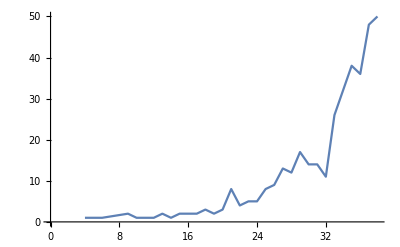

```mathematica
Map[Total,partitions]//Tally//ListLinePlot
```

```mathematica
Select[Map[Select[#,#≠1&]&,partitions],#[[1]]==3&]
```

Part::partw: Part 1 of {} does not exist.

{{3,2},{3,2,2},{3,2,2,2},{3,3,3,2},{3,3,3,2,2}}

```mathematica
Select[Map[Select[#,#≠1&]&,partitions],#[[1]]==2&]
```

Part::partw: Part 1 of {} does not exist.

{{2},{2},{2,2,2}}

```mathematica
Select[Map[Select[#,#≠1&]&,partitions],#[[1]]==4&]
```

Part::partw: Part 1 of {} does not exist.

{{4,3,2},{4,2,2,2},{4,3,2,2},{4,2,2,2,2},{4,3,2,2,2},{4,3,3,3,2},{4,3,3,3,2,2},{4,4,4,3,2},{4,4,4,2,2,2},{4,4,4,3,2,2}}